# Area under the graph (Trapezoidal Rule)

https://www.youtube.com/watch?v=2CaVZyCkcr4

```mathematica
f[x_]:=x^2
```

```mathematica
{a,b,n}={0,4,1000}
```

{0,4,1000}

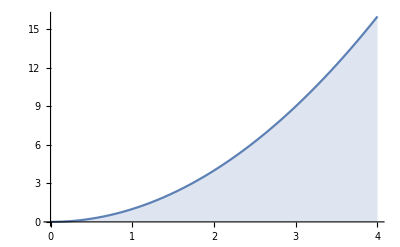

```mathematica
Plot[f[x],{x,a,b},Filling->Bottom]
```

Normal Integration

```mathematica
Integrate[f[x],{x,a,b}]+0.0
```

21.3333

Trapezoidal Rule

```mathematica
h=(b-a)/n
```

1/250

```mathematica
h/2(f[a]+f[b]+2(Sum[f[a+h i],{i,1,n-1}]))+0.0
```

21.3333